```mathematica
OS="win";(*or,linux*)
Needs["ErrorBarPlots`"];
Needs["EDA`"];
Needs["CustomTicks`"];
SetOptions[LinTicks,TickLabelStep->1,MajorTickLength->{0.0125,0},MinorTickLength->{0.0075,0}];
If[OS=="win",
Print["Working Directory: ",descDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\daq-tools-bkg-auto\\nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["C:\\Users\\tmpra\\Dropbox\\Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\Pictures\\nstar\\runs2"];Print["(SysDir) System Directory: ",SysDir="C:\\Users\\tmpra\\Dropbox\\nEDM\\system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="\\";
];
If[OS=="axion",
Print["Working Directory: ",descDir="/home/prajwal/Dropbox/nEDM/daq-tools-bkg-auto/nstar_online"];Print["(AscDir) Rawdata Directory: ",AscDir="/home/prajwal/Dropbox/nEDM/rawdata"];Print["(ScrDir) Scratch Directory: ",curDir=SetDirectory["/home/prajwal/Dropbox/Scratch"]];Print["(PicDir) Picture Directory: ",PicDir="/home/prajwal/Dropbox/nEDM/Pictures/nstar/runs"];Print["(SysDir) System Directory: ",SysDir="/home/prajwal/Dropbox/nEDM/system"];
Print["Rawdata on mpc1636:",mpcDir="/xdata/nedm_data/RawData"];
seperator="/";
];
metaStructure={Word,Real,Real,Word,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Word,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real,Real};
metaStructure2={Number,Number,Number,Number,Number,Number,Number,Word,Real};
metaStructure3={Real,Real,Real,Real,Real,Real,Real};
descdat=ReadList[StringJoin[descDir,seperator,"desc3.dat"],metaStructure2];
metalvl3={Real,Real,Real,Real,Real,Real,Real,Real};
ts={35,50,65,80,95,110,125,140,155,170,180,200,215,220,230,240,245,260,275,280,290,300,305,320,335,340,350,360,365,380};
tssz=Dimensions[ts][[1]];
tsadd=PlusMinus[11.3,0.397];
(*Print["Executing: ts = ",ts[[i]]," , i = ",i];*)
tfal=ReadList[StringJoin[descDir,seperator,"tf-Al.dat"],metaStructure3];
tfcu=ReadList[StringJoin[descDir,seperator,"tf-Cu.dat"],metaStructure3];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
```

Working Directory: C:\Users\tmpra\Dropbox\nEDM\daq-tools-bkg-auto\nstar_online

(AscDir) Rawdata Directory: C:\Users\tmpra\Dropbox\nEDM\rawdata

(ScrDir) Scratch Directory: C:\Users\tmpra\Dropbox\Scratch

(PicDir) Picture Directory: C:\Users\tmpra\Dropbox\nEDM\Pictures\nstar\runs2

(SysDir) System Directory: C:\Users\tmpra\Dropbox\nEDM\system

Rawdata on mpc1636:/xdata/nedm_data/RawData

```mathematica
pttfmual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[2]],tfal[[k]][[4]]}},{k,1,tssz}];
pttfmucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[2]],tfcu[[k]][[4]]}},{k,1,tssz}];
pttf2mual=Table[{{tfal[[k]][[1]],2tsadd[[2]]},{tfal[[k]][[5]],tfal[[k]][[7]]}},{k,1,tssz}];
pttf2mucu=Table[{{tfcu[[k]][[1]],2tsadd[[2]]},{tfcu[[k]][[5]],tfcu[[k]][[7]]}},{k,1,tssz}];
EDAListPlot[pttfmual,pttfmucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","⟨OverBar[t_f]⟩ ± σ(s)"},PlotRange->{{35,420},{0.04,0.09}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
EDAListPlot[pttf2mual,pttf2mucu,Joined->True,Frame->True,FrameLabel->{"t_s(s)","OverBar[⟨SubsuperscriptBox[t, f, 2]⟩/⟨SubscriptBox[t, f]⟩] ± σ(s)"},PlotRange->{{35,420},{0.07,0.13}},PlotLegends->{"Al","Cu"},FrameTicks->LinTicks,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1000},PlotMarkers->{Automatic,Medium}]
```

-Graphics-

-Graphics-

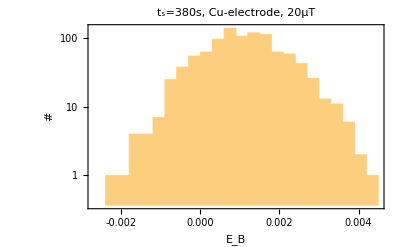

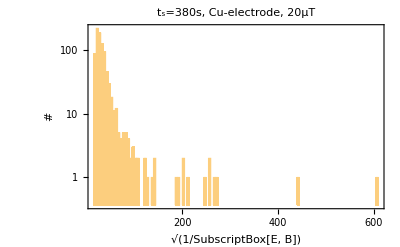

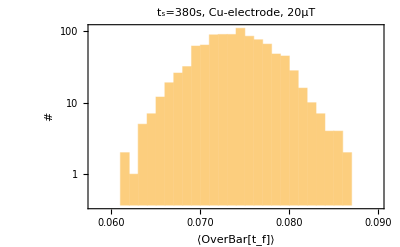

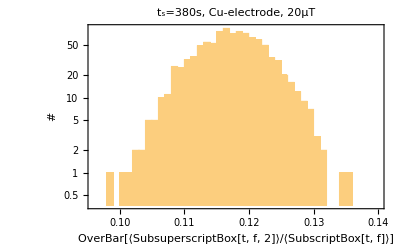

```mathematica
i=16;
lvl3=ReadList[StringJoin[AscDir,seperator,IntegerString[descdat[[i]][[4]],10,6],seperator,IntegerString[descdat[[i]][[4]],10,6],"_lvl3.dat"],metalvl3];
maxsz=1000;
maxsz3=1000;
(*maxsz2=100000;*)
tf=Table[0,{k,1,maxsz}];
tf2tf=Table[0,{k,1,maxsz}];
If[i≤15,
kk=Position[tfal,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfal[[kk]][[2]],tfal[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfal[[kk]][[5]],tfal[[kk]][[7]]],maxsz];
,
kk=Position[tfcu,descdat[[i]][[7]]+2*tsadd[[1]]][[1]][[1]];
tf=RandomVariate[NormalDistribution[tfcu[[kk]][[2]],tfcu[[kk]][[4]]],maxsz];
tf2tf=RandomVariate[NormalDistribution[tfcu[[kk]][[5]],tfcu[[kk]][[7]]],maxsz];
];
(***)
ab=RandomVariate[NormalDistribution[lvl3[[1]][[1]],lvl3[[1]][[2]]],maxsz3];
eb=RandomVariate[NormalDistribution[lvl3[[1]][[3]],lvl3[[1]][[4]]],maxsz3];
(*eb=RandomVariate[NormalDistribution[.0004,.00001],maxsz3];*)
tftseb0=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])*tf2tf]];
tftsab=Flatten[KroneckerProduct[1/ab,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
tftseb=Flatten[KroneckerProduct[1/eb,(descdat[[i]][[7]]+2tsadd[[1]])/tf]];
Histogram[eb,{-.0027,.0045,.0003},PlotRange->Full,PlotRange->Full,Frame->True,FrameLabel->{"E_B","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[Sqrt[1/eb],PlotRange->Full,Frame->True,FrameLabel->{"√(1/SubscriptBox[E, B])","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf,{.058,.09,.001},PlotRange->{{.058,.09},Automatic},Frame->True,FrameLabel->{"⟨OverBar[t_f]⟩","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
Histogram[tf2tf,{.096,.14,.001},PlotRange->{Automatic,Automatic},Frame->True,FrameLabel->{"OverBar[⟨SubsuperscriptBox[t, f, 2]⟩/⟨SubscriptBox[t, f]⟩] ","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]
(*Histogram[Sqrt[tftseb0]]
Histogram[Sqrt[tftsab]]
Histogram[Sqrt[tftseb]]*)
```

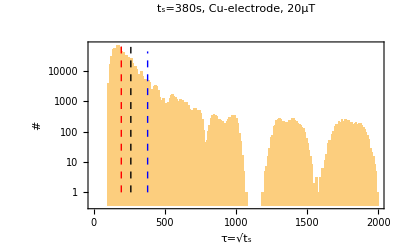

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{379,Log@(10^0)},{379,Log@(10^4.65)}}];
line2=Line[{{261,Log@(10^0)},{261,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^5.0)}}];
tk2[l_,u_,a_,b_,c_,d_,int_]:=SetPrecision[N[Table[{10^j,Superscript["10",j],{a,b}},{j,l,u,int}]~Join~Table[{10^j,"",{c,d}},{j,l-N[Log10[2]],u+N[Log10[2]],int}]],3];
endpt=10000;
(*Histogram[{Sqrt[tftsab],Sqrt[tftseb]},{100,endpt,10},PlotRange->{{100,endpt},Automatic},ChartLegends->{"√(t_s/A_B)","√(t_s/((1 - SubscriptBox[E, B])·SubscriptBox[t, f]))"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],None},{LinTicks,None}},Frame->True,FrameLabel->{"τ/f(η)","#"},TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT"]*)
Show[{Histogram[Sqrt[tftseb0],{100,endpt/5,10},PlotRange->{{0,endpt/5},Automatic},Frame->True,FrameLabel->{"τ=√t_s","#"},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]}]
```

-1.03033×10^6+4782.74 x-8.01519 x^2+0.00721655 x^3-4.07774×10^-6 x^4+1.56857×10^-9 x^5-4.31111×10^-13 x^6+8.72329×10^-17 x^7-1.32227×10^-20 x^8+1.51133×10^-24 x^9-1.29476×10^-28 x^10+8.09139×10^-33 x^11-3.39735×10^-37 x^12+6.61326×10^-42 x^13+2.28926×10^-46 x^14-2.46865×10^-50 x^15+1.05398×10^-54 x^16-2.74354×10^-59 x^17+4.50867×10^-64 x^18-4.32729×10^-69 x^19+1.85742×10^-74 x^20

InterpolatingFunction::dmval: Input value {100.202} lies outside the range of data in the interpolating function. Extrapolation will be used.

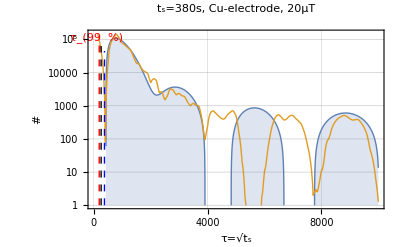

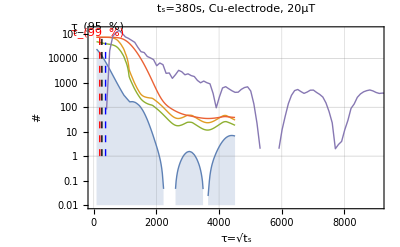

ParallelTable::nopar: No parallel kernels available; proceeding with sequential evaluation.

110

110

90

```mathematica
sigma=10;rr=10;
histlst=HistogramList[Sqrt[tftseb0]];
hstbl=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+5 histlst[[1]][[k]],histlst[[2]][[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
fthst=Fit[hstbl,Table[x^k,{k,0,20,1}],x]
fthst2=Interpolation[hstbl,InterpolationOrder->2];
estbckp=EstimatedBackground[hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm=-EstimatedBackground[-hstbl[[;;,2]],10,Method->{"SNIP",10}];
estbckm2=-EstimatedBackground[-estbckm,10,Method->{"SNIP",10}];
ptbckp=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckp[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
ptbckm2=Table[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],estbckm2[[k]]},{k,1,Dimensions[histlst[[2]]][[1]]}];
Plot[{fthst,fthst2[x]},{x,100,10000},PlotRange->{{0,10000},{1,1.5*10^5}},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
ListLinePlot[{ptbckp,ptbckm,(ptbckp+ptbckm)/2,ptbckm2,hstbl},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotStyle->Thick,Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},PlotLabel->"t_s=380s, Cu-electrode, 20μT",
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{134,Log@(10^5.55)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{124,Log@(10^5.3)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{110,Log@(10^5.05)}],Large]}
}]
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

```mathematica
histhisttftseb0tot=Total[estbckm2];
cumhisttftseb0t=ParallelTable[{(histlst[[1]][[2]]-histlst[[1]][[1]])/2+histlst[[1]][[k]],Total[estbckm2[[;;k]]]/histhisttftseb0tot},{k,1,Dimensions[histlst][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
```

130

130

110

135.6

127.8

115.9

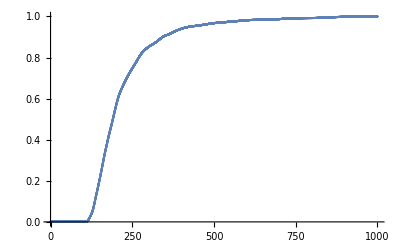

```mathematica
histtftseb0=HistogramList[Sqrt[tftseb0],{0,1000,.1}];
histtftseb0t=Transpose[{(histtftseb0[[1]][[;;-2]]+(histtftseb0[[1]][[2]]-histtftseb0[[1]][[2]])/2),histtftseb0[[2]][[;;]]}];
histhisttftseb0tot=Total[histtftseb0t[[;;,2]]];
cumhisttftseb0t=ParallelTable[{histtftseb0t[[k]][[1]],Total[histtftseb0t[[;;k,2]]]/histhisttftseb0tot},{k,1,Dimensions[histtftseb0t][[1]]}];
val90=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val90]][[1]]]][[1]]
val95=Nearest[cumhisttftseb0t[[;;,2]],0.05][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val95]][[1]]]][[1]]
val99=Nearest[cumhisttftseb0t[[;;,2]],0.01][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val99]][[1]]]][[1]]
ListPlot[cumhisttftseb0t,PlotRange->{{0,1000},{0,1}}]
```

```mathematica
val=Nearest[cumhisttftseb0t[[;;,2]],0.1][[1]];
cumhisttftseb0t[[Flatten[Position[cumhisttftseb0t,val]][[1]]]][[1]]
Sqrt[pttfmucu[[-1]][[2]][[1]]*pttfmucu[[-1]][[1]][[1]]/.00100883]
```

135.6

171.742

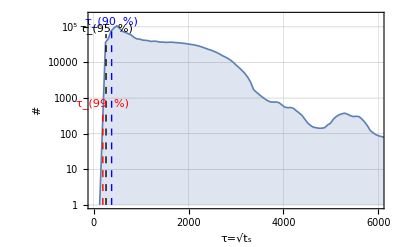

```mathematica
lineStyle1={Thick,Dashed,Blue};
lineStyle2={Thick,Dashed,Black};
lineStyle3={Thick,Dashed,Red};
line1=Line[{{379,Log@(10^0)},{379,Log@(10^5.05)}}];
line2=Line[{{261,Log@(10^0)},{261,Log@(10^4.8)}}];
line3=Line[{{194,Log@(10^0)},{194,Log@(10^2.7)}}];
ListLinePlot[{Join[Table[{10k,.1},{k,0,10}],(ptbckm+hstbl)/2]},Frame->True,FrameLabel->{"τ=√t_s","#"},PlotRange->{{1,5999},{1,2*10^5}},PlotStyle->Thickness[.003],Filling->{1->Axis},ScalingFunctions->{Automatic,"Log"},FrameTicks->{{tk2[0,6,.02,0,0.01,0,1],tk2[0,6,.02,0,0.01,0,1]},{LinTicks,None}},GridLines->Automatic,TicksStyle->Directive[FontSize->40],LabelStyle->{38,Black},FrameTicksStyle->Thick,FrameStyle->Thick,ImageSize->{1200},
Epilog->{
{Directive[lineStyle1],line1,Style[Text["τ_(90  %)",{379,Log@(10^5.15)}],Large]},
{Directive[lineStyle2],line2,Style[Text["τ_(95  %)",{261,Log@(10^4.95)}],Large]},
{Directive[lineStyle3],line3,Style[Text["τ_(99  %)",{194,Log@(10^2.85)}],Large]}
}]
```

```mathematica
Join[Table[{10k,.1},{k,0,10}],ptbckm2]
```

{{0,0.1},{10,0.1},{20,0.1},{30,0.1},{40,0.1},{50,0.1},{60,0.1},{70,0.1},{80,0.1},{90,0.1},{100,0.1},{110,79734.2},{130,79733.9},{150,79733.5},{170,79733.},{190,79732.4},{210,79731.7},{230,79730.8},{250,79729.6},{270,79728.},{290,79726.},{310,79723.5},{330,79720.3},{350,79716.3},{370,79711.},{390,79704.3},{410,79695.2},{430,79683.},{450,79666.6},{470,79647.1},{490,79621.8},{510,79588.2},{530,79542.5},{550,79488.3},{570,79415.9},{590,79327.4},{610,79209.8},{630,79061.9},{650,78865.1},{670,78647.6},{690,78367.},{710,78027.4},{730,77590.7},{750,77074.4},{770,76416.3},{790,75738.6},{810,74904.4},{830,73888.2},{850,72672.6},{870,71451.1},{890,70052.},{910,68482.2},{930,66629.},{950,64833.7},{970,62766.},{990,60714.},{1010,58388.1},{1030,56129.1},{1050,53699.7},{1070,51390.2},{1090,48967.2},{1110,46464.4},{1130,43835.3},{1150,41381.3},{1170,38855.3},{1190,36485.1},{1210,34040.9},{1230,31788.8},{1250,29591.7},{1270,27478.6},{1290,25455.2},{1310,23531.2},{1330,21702.8},{1350,19975.2},{1370,18341.9},{1390,16807.3},{1410,15365.3},{1430,14019.},{1450,12761.3},{1470,11593.3},{1490,10507.5},{1510,9505.31},{1530,8579.63},{1550,7729.7},{1570,6948.33},{1590,6234.61},{1610,5581.35},{1630,4987.63},{1650,4447.01},{1670,3958.52},{1690,3515.89},{1710,3118.26},{1730,2759.59},{1750,2438.78},{1770,2150.75},{1790,1894.39},{1810,1665.33},{1830,1462.45},{1850,1281.82},{1870,1122.55},{1890,981.393},{1910,857.737},{1930,748.708},{1950,653.607},{1970,570.082},{1990,497.609},{2010,434.267},{2030,379.674},{2050,332.197},{2070,291.429},{2090,256.051},{2110,225.749},{2130,199.479},{2150,177.039},{2170,157.633},{2190,141.077},{2210,126.744},{2230,114.488},{2250,103.854},{2270,94.7607},{2290,86.8661},{2310,80.0995},{2330,74.1436},{2350,68.9549},{2370,64.3586},{2390,60.3222},{2410,56.7029},{2430,53.4715},{2450,50.5013},{2470,47.7707},{2490,45.2355},{2510,42.8837},{2530,40.6839},{2550,38.6284},{2570,36.6934},{2590,34.874},{2610,33.1528},{2630,31.5256},{2650,29.9794},{2670,28.5114},{2690,27.1113},{2710,25.7775},{2730,24.5021},{2750,23.2844},{2770,22.1183},{2790,21.0032},{2810,19.9345},{2830,18.9115},{2850,17.9306},{2870,16.9915},{2890,16.0913},{2910,15.2298},{2930,14.4048},{2950,13.6158},{2970,12.8611},{2990,12.1403},{3010,11.452},{3030,10.7958},{3050,10.1703},{3070,9.57533},{3090,9.00957},{3110,8.47278},{3130,7.96386},{3150,7.48255},{3170,7.02783},{3190,6.59946},{3210,6.19649},{3230,5.81872},{3250,5.46523},{3270,5.13587},{3290,4.82977},{3310,4.54687},{3330,4.28628},{3350,4.04804},{3370,3.83126},{3390,3.63607},{3410,3.46158},{3430,3.308},{3450,3.17448},{3470,3.06133},{3490,2.96768},{3510,2.89396},{3530,2.83929},{3550,2.80422},{3570,2.78783},{3590,2.79081},{3610,2.81221},{3630,2.8528},{3650,2.91161},{3670,2.98954},{3690,3.08554},{3710,3.20063},{3730,3.33471},{3750,3.48801},{3770,3.66031},{3790,3.85192},{3810,4.06247},{3830,4.2923},{3850,4.54189},{3870,4.81078},{3890,5.09915},{3910,5.40659},{3930,5.73405},{3950,6.08226},{3970,6.4513},{3990,6.8407},{4010,7.25114},{4030,7.68116},{4050,8.13207},{4070,8.60334},{4090,9.09527},{4110,9.60606},{4130,10.14},{4150,10.6937},{4170,11.2696},{4190,11.8647},{4210,12.4803},{4230,13.1139},{4250,13.7693},{4270,14.4409},{4290,15.137},{4310,15.8481},{4330,16.583},{4350,17.3306},{4370,18.0999},{4390,18.8778},{4410,19.6822},{4430,20.4995},{4450,21.3384},{4470,22.1862},{4490,23.0473},{4510,23.9138},{4530,24.807},{4550,25.7121},{4570,26.6327},{4590,27.5598},{4610,28.4925},{4630,29.4256},{4650,30.3941},{4670,31.3631},{4690,32.3321},{4710,33.3011},{4730,34.2923},{4750,35.2866},{4770,36.2809},{4790,37.1597},{4810,37.909},{4830,38.5248},{4850,39.0103},{4870,39.3694},{4890,39.5997},{4910,39.7019},{4930,39.6775},{4950,39.528},{4970,39.2516},{4990,38.8854},{5010,38.5192},{5030,38.1549},{5050,37.8064},{5070,37.4666},{5090,37.1269},{5110,36.8003},{5130,36.4911},{5150,36.195},{5170,35.899},{5190,35.6108},{5210,35.3375},{5230,35.0801},{5250,34.8398},{5270,34.6084}}

## Simply Playing!

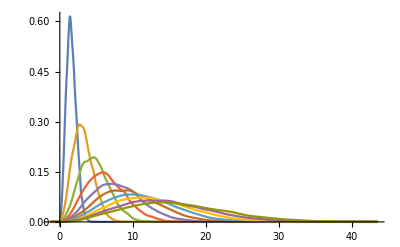

```mathematica
SmoothHistogram[Table[RandomVariate[MaxwellDistribution[k],10000],{k,1,10}],PlotRange->Full]
```

```mathematica
maxn=100000;
For[i=1,i≤ 10,i++,
randr=RandomVariate[MaxwellDistribution[1],maxn];
randt=RandomReal[{0,2Pi},2*maxn];
Print[Norm[Map[Mean,Table[{randr[[k]]Cos[randt[[k]]],randr[[k]]Sin[randt[[k]]]Cos[randt[[maxn+k]]],randr[[k]]Sin[randt[[k]]]Sin[randt[[maxn+k]]]},{k,1,maxn}]]]];
];//AbsoluteTiming
```

182.559

182.31

182.495

182.937

182.467

182.962

182.607

182.637

182.715

182.648

{10.1779,Null}

```mathematica
Map[Norm,Table[{k,2k,3k},{k,1,10}]]
```

{√14,2 √14,3 √14,4 √14,5 √14,6 √14,7 √14,8 √14,9 √14,10 √14}

```mathematica
{46.331984274390216,Null}
```